C:\Users\aoubl\Desktop\rho-c.xlsx

C:\Users\aoubl\Desktop\sigma-c.xlsx

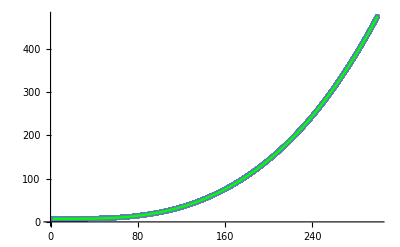

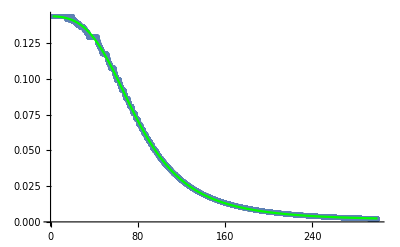

{{50.,0.00381},{40.,0.00332},{30.,0.00294},{25.,0.00258},{20.,0.00234},{15.,0.00218},{10.,0.00193},{8.,0.00177},{4.,0.0018},{2.,0.00206}}

{ρ→0.683869,σ→0.,m→-0.00805732}

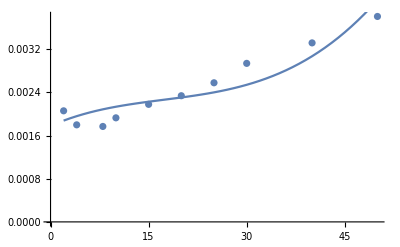

ListPlot::lpn: Damping`data 不是由数字或者数对组成的列表.

Show::gcomb: 无法合并 Show[,ListPlot[Damping`data,PlotStyle→{GrayLevel[0],PointSize[Large]}],Frame→True] 中的图形对象.

ListPlot::lpn: Damping`data 不是由数字或者数对组成的列表.

Show::gcomb: 无法合并 Show[,ListPlot[Damping`data,PlotStyle→{GrayLevel[0],PointSize[Large]}],Frame→True] 中的图形对象.

ListPlot::lpn: Damping`data 不是由数字或者数对组成的列表.

Show::gcomb: 无法合并 Show[,ListPlot[Damping`data,PlotStyle→{GrayLevel[0],PointSize[Large]}],Frame→True] 中的图形对象.

```mathematica
(*电导率和电阻率的结合来拟合damping*)Clear[T]
Clear["Gloal`*"];Clear[rho`T];Clear[sigma`T];t=100;T`start=2;T`stop=0;
data=Import["C:\\Users\\aoubl\\Desktop\\Fit data\\CrO2 data\\c-axis-resistivity and conductivity.xlsx","EmptyField"->"Empty"];
data=data[[1]];
data=Transpose@data;
T`data=data[[1]];
rho`raw`data=data[[2]];
sigma`raw`data=data[[3]];
T0=0;
resis`fun[a_,b_,c_,d_,e_,f_,T_,T0_]:=a+b*(T-T0)+c*(T-T0)^2+d*(T-T0)^3+e*(T-T0)^4+f*(T-T0)^5;
condu`fun[a_,b_,c_,d_,e_,f_,T_,T0_]=1/resis`fun[a,b,c,d,e,f,T,T0];
resis`data=Table[{T`data[[i]],rho`raw`data[[i]]},{i,Length@T`data}];
condu`data=Table[{T`data[[i]],sigma`raw`data[[i]]},{i,Length@T`data}];
fit`res=FindFit[resis`data,resis`fun[a,b,c,d,e,f,T,T0],{a,b,c,d,e,f},T];
fit`con=FindFit[condu`data,condu`fun[a,b,c,d,e,f,T,T0],{a,b,c,d,e,f},T];
rho`fit`data=Table[{T,resis`fun[a,b,c,d,e,f,T,T0]/.fit`res},{T,2,300,0.5}];
Export["C:\\Users\\aoubl\\Desktop\\CrO2 Fit data\\rho-c.xlsx",rho`fit`data]

sigma`fit`data=Table[{T,condu`fun[a,b,c,d,e,f,T,T0]/.fit`con},{T,2,300,0.5}];
Export["C:\\Users\\aoubl\\Desktop\\CrO2 Fit data\\sigma-c.xlsx",sigma`fit`data]
Show[{ListPlot[resis`data,PlotMarkers->{Automatic,5}],ListLinePlot[rho`fit`data,PlotStyle->{Green}]}]
Show[{ListPlot[condu`data,PlotMarkers->{Automatic,5}],ListLinePlot[sigma`fit`data,PlotStyle->{Green}]}]

(*T`new`data=Select[T`data,T`stop>=#>=T`start&];
lin`start=First@Flatten@Position[T`data,T`new`data[[1]]]
lin`stop=First@Flatten@Position[T`data,T`new`data[[-1]]]
rho`raw`data=Take[rho`raw`data,{lin`start,lin`stop}];
sigma`raw`data=Take[sigma`raw`data,{lin`start,lin`stop}];*)
(*先拟合电阻率和电导率*)
resis`like[T_,T0_]:=((resis`fun[a,b,c,d,e,f,T,T0]/resis`fun[a,b,c,d,e,f,300,T0])/.fit`res);
condu`like[T_,T0_]:=((condu`fun[a,b,c,d,e,f,T,T0]/condu`fun[a,b,c,d,e,f,300,T0])/.fit`con);
cc[ρ_,σ_,m_,T_,T0_]:=ρ*resis`like[T,T0]+σ*condu`like[T,T0]+m;
T`start=2;T`stop=300;
If[T`stop≤100,
Damping`data=Table[{data[[7]][[i]],data[[8]][[i]]},{i,Length@data[[7]]}],Damping`data=Table[{data[[4]][[i]],data[[5]][[i]]},{i,Length@data[[4]]}]];
Damping`data=Take[Damping`data,{7,16}]
damping`fit=FindFit[Damping`data,{cc[ρ,σ,m,T,T0],ρ>0,σ==0},{{ρ,0},{σ,0},m},T]
damping`fit`data=Table[{T,cc[ρ,σ,m,T,T0]/.damping`fit},{T,2,300,1}];
(*resis`like`data=Table[{T,(ρ*resis`like[T,T0])/.damping`fit},{T,50,300,1}];
condu`like`data=Table[{T,(σ*condu`like[T,T0])/.damping`fit},{T,50,300,1}];*)
Show[ListPlot@Damping`data,ListLinePlot@damping`fit`data]


fitting`data[a_,b_]:=a*rho`raw`data+b*sigma`raw`data;
rho`data[a_]:=a*rho`raw`data;
sigma`data[b_]:=b*sigma`raw`data;

fitting`T[a_,b_]:=Table[{T`data[[i]],fitting`data[a,b][[i]]},{i,Length@T`data}];
rho`T[a_]:=Table[{T`data[[i]],rho`data[a][[i]]},{i,Length@T`data}];
sigma`T[b_]:=Table[{T`data[[i]],sigma`data[b][[i]]},{i,Length@T`data}];
If[T`stop≤100,
Damping`data=Table[{data[[7]][[i]],data[[8]][[i]]},{i,Length@data[[7]]}],Damping`data=Table[{data[[4]][[i]],data[[5]][[i]]},{i,Length@data[[4]]}]];
Manipulate[Show[ListLinePlot[{fitting`T[a,b],rho`T[a],sigma`T[b]},PlotStyle->{Blue,{Red,Dashed},{Gray,Dashed}},PlotLegends->{"Fitting","ρ-like","σ-like"}],ListPlot[Damping`data,PlotStyle->{Black,PointSize[Large]}],Frame->True],
{{a,2.301,"Resitivity term"},0,10,0.001},{{b,0.0001,"Conductivity term"},0,0.001,0.0001}]
```